## 1465

```mathematica
a={{2,-1,2},{5,-3,3},{-1,0,-2}}
```

{{2,-1,2},{5,-3,3},{-1,0,-2}}

```mathematica
MatrixForm[a]
```

(2 | -1 | 2
5 | -3 | 3
-1 | 0 | -2)

```mathematica
({{2, -1, 2}, {5, -3, 3}, {-1, 0, -2}})
```

{{2,-1,2},{5,-3,3},{-1,0,-2}}

```mathematica
Det[a]
```

-1

```mathematica
i=IdentityMatrix[3]
```

{{1,0,0},{0,1,0},{0,0,1}}

```mathematica
Solve[Det[a-l*i]==0]
```

{{l→-1},{l→-1},{l→-1}}

```mathematica
x={x1,x2,x3}
```

{x1,x2,x3}

```mathematica
MatrixForm[x]
```

(x1
x2
x3)

```mathematica
Solve[(a-(-1)*i).x==0]
```

{{x2→x1,x3→-x1}}

## 1474

```mathematica
a={{3,-1,0,0},{1,1,0,0},{3,0,5,-3},{4,-1,3,-1}}
```

{{3,-1,0,0},{1,1,0,0},{3,0,5,-3},{4,-1,3,-1}}

```mathematica
MatrixForm[a]
```

```mathematica
({{3, -1, 0, 0}, {1, 1, 0, 0}, {3, 0, 5, -3}, {4, -1, 3, -1}})
```

```mathematica
i=IdentityMatrix[4]
```

{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}

```mathematica
Solve[Det[a-l*i]==0]
```

{{l→2},{l→2},{l→2},{l→2}}

```mathematica
x={x1,x2,x3,x4}
```

{x1,x2,x3,x4}

```mathematica
Solve[(a-2*i).x==0]
```

{{x2→x1,x4→x1+x3}}

# 1494

```mathematica
a={{1,0,2,-1},{0,1,4,-2},{2,-1,0,1},{2,-1,-1,2}};
MatrixForm[a]
```

(1 | 0 | 2 | -1
0 | 1 | 4 | -2
2 | -1 | 0 | 1
2 | -1 | -1 | 2)

```mathematica
i=IdentityMatrix[4]
```

{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}

```mathematica
Solve[Det[a-l*i]==0]
```

```mathematica
{{l->1},{l->1},{l->1},{l->1}}
```

```mathematica
x={x1,x2,x3,x4}
```

{x1,x2,x3,x4}

```mathematica
Solve[(a-1*i).x==0]
```

{{x3→-2 x1+x2,x4→-4 x1+2 x2}}

# 1504

```mathematica
a= {{4,-2,2},{2,0,2},{-1,1,1}};
```

```mathematica
MatrixForm[a]
```

(4 | -2 | 2
2 | 0 | 2
-1 | 1 | 1)

```mathematica
i = IdentityMatrix[3]
```

{{1,0,0},{0,1,0},{0,0,1}}

```mathematica
Solve[Det[a-i*k]==0]
```

{{k→1},{k→2},{k→2}}

```mathematica
x={x1,x2,x3}
```

{x1,x2,x3}

```mathematica
Solve[(a-1*i).x ==0]
```

{{x2→x1,x3→-x1/2}}

```mathematica
Solve[(a-2*i).x==0]
```

{{x3→-x1+x2}}

# 13.04.17

```mathematica
k:=2;
t:=3;
α:=-4;
β:=1;
c=IntegerDigits[i,k];
B=Table[0,{i,1,2^t(β-α+1)},{j,1,2}]
```

{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}}

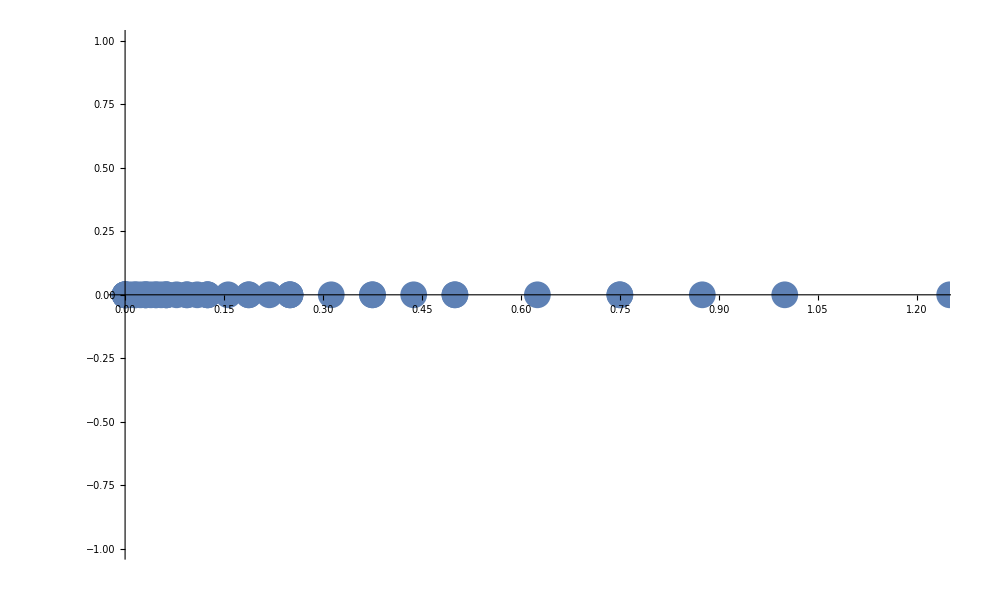

```mathematica
For[γ=α,γ≤β,γ++,
For[i=0,i≤2^t-1,i++,c=IntegerDigits[i,k];d=Table[0,{j,t}];For[j=1,j≤Length[c],j++,d⟦t-Length[c]+j⟧=c⟦j⟧];(*Print[d,c];*)
B⟦  2^t(γ-α)+i+1,1⟧=Sum[d⟦j⟧/k^j,{j,1,t}] k^γ;];
]
ListLinePlot[B,Joined->False]
```

```mathematica
B
```

{{0,0},{1/16,0},{1/8,0},{3/16,0},{1/4,0},{5/16,0},{3/8,0},{7/16,0},{0,0},{1/8,0},{1/4,0},{3/8,0},{1/2,0},{5/8,0},{3/4,0},{7/8,0},{0,0},{1/4,0},{1/2,0},{3/4,0},{1,0},{5/4,0},{3/2,0},{7/4,0},{0,0},{1/2,0},{1,0},{3/2,0},{2,0},{5/2,0},{3,0},{7/2,0}}